1

0.5

2.3

0.5

0.75

100

{{e1→InterpolatingFunction[…],e2→InterpolatingFunction[…],i1→InterpolatingFunction[…],i2→InterpolatingFunction[…],o1→InterpolatingFunction[…]}}

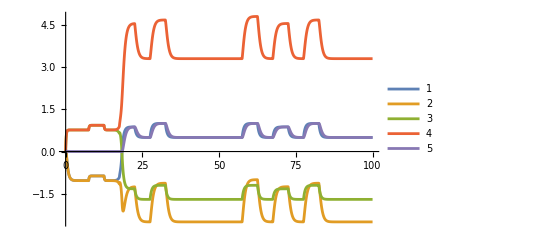

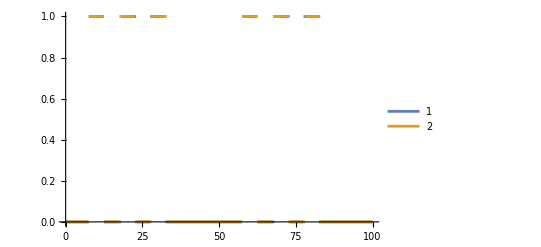

```mathematica
gee=2.;
gii =2.;
gei=2;1.75;
gie=2;1.75;
go=1
be=.5
bi =2.3
s=.5
time =40;
Relu[x_]:=Piecewise[{{0,x<=0},{x,0<x<2},{2,x>=2}}]
Δ=.75



in1[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] +Δ HeavisidePi[(t-20)/dur] + HeavisidePi[(t-30)/dur] 
in2[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] + HeavisidePi[(t-20)/dur] +Δ HeavisidePi[(t-30)/dur] 
in1t[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] + HeavisidePi[(t-Δ-20)/dur] + HeavisidePi[(t-30)/dur] 
in2t[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] + HeavisidePi[(t-20)/dur] + HeavisidePi[(t-Δ-30)/dur] 
time =100

sol4=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *in1[t][Δ,5]+s in1[t-50][Δ,5], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*in2[t][Δ,5]+s in2[t-50][Δ,5], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*in1[t][Δ,5]+s in1[t-50][Δ,5], i1[0]==0.01,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*in2[t][Δ,5]+s in2[t-50][Δ,5], i2[0]==0.01,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"BDF"]
Plot[{e1[t]/.sol4,e2[t]/.sol4,i1[t]/.sol4,i2[t]/.sol4,o1[t]/.sol4},{t,0,time},PlotRange->All,PlotLegends->Automatic]
Plot[{in1t[t][.5,5]+in1t[t-50][.5,5],in2t[t][.5,5]+in2t[t-50][.5,5]},{t,0,time},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
n=50;
Δ=1000;

m=Table[Table[Sin[1.i-k],{i,0,n}],{k,1,5}];
mtimed= Table[Table[{Δ i,Sin[1.i-k]},{i,0,n}],{k,1,5}];
mtimed= Table[Table[{t,1.Sin[(π t/400)+π k/10]HeavisideTheta[t-00.1]},{t,0,2000,1}],{k,1,10}]
MatrixForm/@m;
m//MatrixForm
pix=Table[Interpolation[mtimed[[k]],InterpolationOrder->0],{k,1,5}]
```

(-0.841471 | 0. | 0.841471 | 0.909297 | 0.14112 | -0.756802 | -0.958924 | -0.279415 | 0.656987 | 0.989358 | 0.412118 | -0.544021 | -0.99999 | -0.536573 | 0.420167 | 0.990607 | 0.650288 | -0.287903 | -0.961397 | -0.750987 | 0.149877 | 0.912945 | 0.836656 | -0.00885131 | -0.84622 | -0.905578 | -0.132352 | 0.762558 | 0.956376 | 0.270906 | -0.663634 | -0.988032 | -0.404038 | 0.551427 | 0.999912 | 0.529083 | -0.428183 | -0.991779 | -0.643538 | 0.296369 | 0.963795 | 0.745113 | -0.158623 | -0.916522 | -0.831775 | 0.0177019 | 0.850904 | 0.901788 | 0.123573 | -0.768255 | -0.953753
-0.909297 | -0.841471 | 0. | 0.841471 | 0.909297 | 0.14112 | -0.756802 | -0.958924 | -0.279415 | 0.656987 | 0.989358 | 0.412118 | -0.544021 | -0.99999 | -0.536573 | 0.420167 | 0.990607 | 0.650288 | -0.287903 | -0.961397 | -0.750987 | 0.149877 | 0.912945 | 0.836656 | -0.00885131 | -0.84622 | -0.905578 | -0.132352 | 0.762558 | 0.956376 | 0.270906 | -0.663634 | -0.988032 | -0.404038 | 0.551427 | 0.999912 | 0.529083 | -0.428183 | -0.991779 | -0.643538 | 0.296369 | 0.963795 | 0.745113 | -0.158623 | -0.916522 | -0.831775 | 0.0177019 | 0.850904 | 0.901788 | 0.123573 | -0.768255
-0.14112 | -0.909297 | -0.841471 | 0. | 0.841471 | 0.909297 | 0.14112 | -0.756802 | -0.958924 | -0.279415 | 0.656987 | 0.989358 | 0.412118 | -0.544021 | -0.99999 | -0.536573 | 0.420167 | 0.990607 | 0.650288 | -0.287903 | -0.961397 | -0.750987 | 0.149877 | 0.912945 | 0.836656 | -0.00885131 | -0.84622 | -0.905578 | -0.132352 | 0.762558 | 0.956376 | 0.270906 | -0.663634 | -0.988032 | -0.404038 | 0.551427 | 0.999912 | 0.529083 | -0.428183 | -0.991779 | -0.643538 | 0.296369 | 0.963795 | 0.745113 | -0.158623 | -0.916522 | -0.831775 | 0.0177019 | 0.850904 | 0.901788 | 0.123573
0.756802 | -0.14112 | -0.909297 | -0.841471 | 0. | 0.841471 | 0.909297 | 0.14112 | -0.756802 | -0.958924 | -0.279415 | 0.656987 | 0.989358 | 0.412118 | -0.544021 | -0.99999 | -0.536573 | 0.420167 | 0.990607 | 0.650288 | -0.287903 | -0.961397 | -0.750987 | 0.149877 | 0.912945 | 0.836656 | -0.00885131 | -0.84622 | -0.905578 | -0.132352 | 0.762558 | 0.956376 | 0.270906 | -0.663634 | -0.988032 | -0.404038 | 0.551427 | 0.999912 | 0.529083 | -0.428183 | -0.991779 | -0.643538 | 0.296369 | 0.963795 | 0.745113 | -0.158623 | -0.916522 | -0.831775 | 0.0177019 | 0.850904 | 0.901788
0.958924 | 0.756802 | -0.14112 | -0.909297 | -0.841471 | 0. | 0.841471 | 0.909297 | 0.14112 | -0.756802 | -0.958924 | -0.279415 | 0.656987 | 0.989358 | 0.412118 | -0.544021 | -0.99999 | -0.536573 | 0.420167 | 0.990607 | 0.650288 | -0.287903 | -0.961397 | -0.750987 | 0.149877 | 0.912945 | 0.836656 | -0.00885131 | -0.84622 | -0.905578 | -0.132352 | 0.762558 | 0.956376 | 0.270906 | -0.663634 | -0.988032 | -0.404038 | 0.551427 | 0.999912 | 0.529083 | -0.428183 | -0.991779 | -0.643538 | 0.296369 | 0.963795 | 0.745113 | -0.158623 | -0.916522 | -0.831775 | 0.0177019 | 0.850904)

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
time =1200
Fv[V_,W_][Ii_,k_,b_]:=-3V+((1/k)*V^2 +40+100b-W+Ii)
Fw[V_,W_][a_,b_]:=a (b(V)-W)
Iinj [start_,dur_][t_]:=HeavisidePi[(t-start)/dur-1/2]
T[x_]:=Transpose[x]
L[x_]:=Length[x]
(*base parameters of the neurons*)
k = 25;
a =1/10.;
b=.2;
c= 10;
d =.01;
tau =10;

(*synaptic weights*)
go=4;
gee = 2;
gei = 5;
gie = -10;
gii = -10;

ClassicalRungeKuttaCoefficients[4,prec_]:=With[{amat={{1/2},{0,1/2},{0,0,1}},bvec={1/6,1/3,1/3,1/6},cvec={1/2,1/2,1}},N[{amat,bvec,cvec},prec]]


input1[t_]:=1Sin[π t/400]HeavisideTheta[t-00.1]
inputAnti[t_]:=1Sin[(π (t-400) /400)]HeavisideTheta[t-00.1]
inputAdv[t_]:=1Sin[(π (t-50) /400)]HeavisideTheta[t-00.1]
inputLag[t_]:=1Sin[(π (t+50) /400)]HeavisideTheta[t-00.1]

Ibias={2,2,2.5,2.5,1.1}
solSyncAND=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+input1[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+input1[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];

solAntiAND=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+inputAnti[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+inputAnti[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];
Print["Done"]
```

1200

{2,2,2.5,2.5,1.1}

Done

```mathematica
Ibias={0,1.5,2.5,2.5,2}
solSyncAND=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+input1[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+input1[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];
```

{0,1.5,2.5,2.5,2}

Image Detector

```mathematica
shift=0
pixel=1
pixsh
time=2000
Ibias={2,2,2.5,2.5,1.1}
Ibias={0,1.5,2.5,2.5,2}
Monitor[solDetection=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+pix[[pixel]][t+shift]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+pix[[pixel]][t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+pix[[pixel]][t+shift]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+pix[[pixel]][t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"FixedStep","StepSize"->0.1,"Method"->{"ExplicitRungeKutta"}},Compiled->True,EvaluationMonitor:>(monitor=t)];,monitor]
monitor

Print["Done"]



shift=20
pixel=1
time=2000
Ibias={2,2,2.5,2.5,1.1}
Ibias={1.5+1,0+1,2.5,2.5,2}



Monitor[solDetectionO=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+pix[[pixel]][t+shift]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+pix[[pixel]][t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+pix[[pixel]][t+shift]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+pix[[pixel]][t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"FixedStep","StepSize"->0.1,"Method"->{"ExplicitRungeKutta"}},Compiled->True,EvaluationMonitor:>(monitor=t)];,monitor]
monitor

Print["Done"]
```

-20

1

2000

{2,2,2.5,2.5,1.1}

{0.2,1.7,2.7,1.7,3.2}

InterpolatingFunction::dmval: Input value {-20.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-19.996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2000.

Done

20

1

2000

{2,2,2.5,2.5,1.1}

{2.5,1,2.5,2.5,2}

InterpolatingFunction::dmval: Input value {2000.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2000.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2000.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2000.

Done

```mathematica
Sum[((4.)/5^i),{i,1,3}]
```

0.992

```mathematica
.8+4./25+4/125
```

0.992

```mathematica
shift=20
pixel=1
time=2000
Ibias={2,2,2.5,2.5,1.1}
Ibias={1.5,0,2.5,2.5,2-1}+1



Monitor[solDetectionO=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+pix[[pixel]][t+shift]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+pix[[pixel]][t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+pix[[pixel]][t+shift]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+pix[[pixel]][t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"FixedStep","StepSize"->0.1,"Method"->{"ExplicitRungeKutta"}},Compiled->True,EvaluationMonitor:>(monitor=t)];,monitor]
monitor

Print["Done"]
```

20

1

2000

{2,2,2.5,2.5,1.1}

{2.5,1,3.5,3.5,2}

InterpolatingFunction::dmval: Input value {2000.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2000.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2000.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2000.

Done